## Gamma function

```mathematica
Remove["Global`*"]
```

the values of the Gamma function

```mathematica
Table[Gamma[n],{n,1,10}]
```

{1,1,2,6,24,120,720,5040,40320,362880}

the values of the function (n-1)!

```mathematica
Table[Factorial[n-1],{n,1,10}]
```

{1,1,2,6,24,120,720,5040,40320,362880}

```mathematica
Table[test = 1;While[l>0,test = test*l;l=l-1];Print[test],{l,0,9}];
```

1

1

2

6

24

120

720

5040

40320

362880

the gamma function in it’s integral representation

```mathematica
Table[NIntegrate[{t^(z-1)*Exp[-t]},{t,0,Infinity}],{z,1,10}]
```

{{1.},{1.},{2.},{6.},{24.},{120.},{720.},{5040.},{40320.},{362880.}}

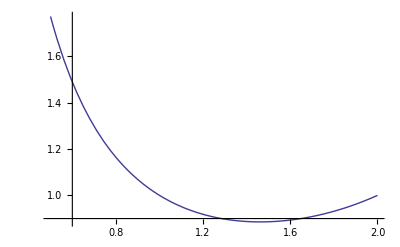

```mathematica
Plot[NIntegrate[{t^(z-1)*Exp[-t]},{t,0,Infinity}],{z,0.5,2}]
```

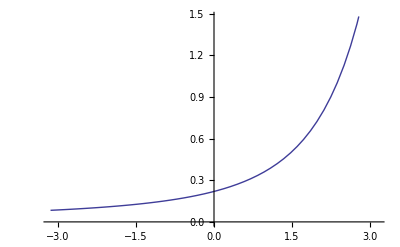

```mathematica
Plot[Integrate[{t^(z-1)*Exp[-t]},{t,1,Infinity}],{z,-Pi,Pi}]
```

establishing the sterling’s approximation

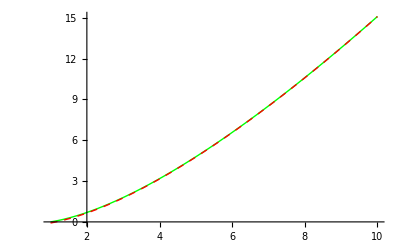

```mathematica
Show[Plot[Log[Gamma[N+1]],{N,1,10},PlotStyle->{Green}],Plot[N*Log[N]-N+1/2*Log[2*Pi*N],{N,1,10},PlotStyle->{Red, Dashed}]]
```

estimating the volume of a d-dim sphere

```mathematica
Table[{Pi^(N/2)*R^N/Gamma[N/2+1]},{N,2,4}]
```

{{π R^2},{(4 π R^3)/3},{(π^2 R^4)/2}}

showing that the volume of a d-dim sphere of radius = 1 increases and then decreases

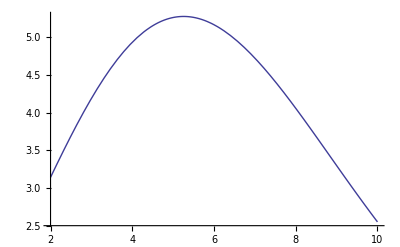

```mathematica
R=1;Plot[{Pi^(N/2)*R^N/Gamma[N/2+1]},{N,2,10}]
```

estimating the surface area of a d-dim sphere

```mathematica
Table[D[Pi^(N/2)*r^N/Gamma[N/2+1],r],{N,2,4}]
```

{2 π r,4 π r^2,2 π^2 r^3}

## Legendre Polynomials

```mathematica
Remove["Global`*"]
```

the legendre polynomials are one of the solutions of the differential equation

```mathematica
DSolve[{D[Sin[θ]*D[y,θ],θ]==-l*(l+1)*Sin[θ]*y[θ],y[θ_]==LegendreP[l,Cos[θ]]},y[θ],θ]
```

{}

```mathematica
DSolve[{D[Sin[θ]*y'[θ],θ]==-l*(l+1)*Sin[θ]*y[θ],y[θ_]==LegendreP[l,Cos[θ]]},y[θ],θ]
```

DSolve::deqn: Equation or list of equations expected instead of LegendreP[l, Cos[θ]] in the first argument {-Cos[θ]\ ((-1 + Times[« 2 »])\ Cos[θ]\ LegendreP[l, Cos[« 1 »]] + (1 + l)\ LegendreP[Plus[« 2 »], Cos[« 1 »]])\ Sin[θ]/-1 + Cos[« 1 »]^2 + Sin[θ]\ (-Cos[θ]\ (Times[« 3 »] + Times[« 2 »])/Plus[« 2 »] - 2\ Cos[θ]\ « 1 »\ Sin[« 1 »]^2/Plus[« 1 »]^2 - Sin[θ]\ (« 1 »)/Plus[« 2 »]) == -l\ (1 + l)\ « 1 »\ Sin[θ], « 9 »[« 1 »]}.

DSolve[{Cos[θ] y'[θ]+Sin[θ] y''[θ]==-l (1+l) Sin[θ] y[θ],LegendreP[l,Cos[θ]]},LegendreP[l,Cos[θ]],θ]

verifying the rodrigues formula

```mathematica
Table[LegendreP[l,x],{l,1,5}]
```

{x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4),1/8 (15 x-70 x^3+63 x^5)}

```mathematica
Table[temp=l;diff= (x^2-1)^l;While[temp>0,diff=D[diff,x];temp=temp-1];Print[Simplify[(1/(2^l*Factorial[l]))*diff]],{l,1,5}];
```

x

1/2 (-1+3 x^2)

1/2 x (-3+5 x^2)

1/8 (3-30 x^2+35 x^4)

1/8 x (15-70 x^2+63 x^4)

establishing the orthogonality of the legendre polynomials

```mathematica
Table[Table[Integrate[LegendreP[l,x]*LegendreP[l1,x],{x,-1,1}],{l1,0,2}],{l,0,2}]
```

{{2,0,0},{0,2/3,0},{0,0,2/5}}

```mathematica
Table[Table[NIntegrate[LegendreP[l,x]*LegendreP[l1,x],{x,-1,1}],{l1,0,2}],{l,0,2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.925766}. NIntegrate obtained -2.94903×10^-17 and 8.05223×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.925766}. NIntegrate obtained -2.94903×10^-17 and 8.05223×10^-17 for the integral and error estimates.

{{2.,0.,-2.94903×10^-17},{0.,0.666667,0.},{-2.94903×10^-17,0.,0.4}}

```mathematica
Table[Table[2/(2*l+1)*KroneckerDelta[l,l1],{l1,0,2}],{l,0,2}]
```

{{2,0,0},{0,2/3,0},{0,0,2/5}}

question #4

question #5

question #6

## Spherical Harmonics

```mathematica
Remove["Global`*"]
```

verifying that the spherical harmonic function Y can be written in terms of the associated legendre polynomial P

```mathematica
Table[Table[(-1)^m*√((2*l+1)/(4*Pi)*Factorial[l-m]/Factorial[l+m])*LegendreP[l,m,Cos[θ]]*Exp[I*m*ϕ],{m,-l,l}],{l,0,2}]
```

{{1/(2 √π)},{-1/2 ⅇ^(-ⅈ ϕ) √(3/(2 π)) √(1-Cos[θ]^2),1/2 √(3/π) Cos[θ],1/2 ⅇ^(ⅈ ϕ) √(3/(2 π)) √(1-Cos[θ]^2)},{1/4 ⅇ^(-2 ⅈ ϕ) √(15/(2 π)) (1-Cos[θ]^2),-1/2 ⅇ^(-ⅈ ϕ) √(15/(2 π)) Cos[θ] √(1-Cos[θ]^2),1/4 √(5/π) (-1+3 Cos[θ]^2),1/2 ⅇ^(ⅈ ϕ) √(15/(2 π)) Cos[θ] √(1-Cos[θ]^2),-1/4 ⅇ^(2 ⅈ ϕ) √(15/(2 π)) (-1+Cos[θ]^2)}}

```mathematica
Table[Table[SphericalHarmonicY[l,m,θ,ϕ],{m,-l,l}],{l,0,2}]
```

{{1/(2 √π)},{1/2 ⅇ^(-ⅈ ϕ) √(3/(2 π)) Sin[θ],1/2 √(3/π) Cos[θ],-1/2 ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ]},{1/4 ⅇ^(-2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2,1/2 ⅇ^(-ⅈ ϕ) √(15/(2 π)) Cos[θ] Sin[θ],1/4 √(5/π) (-1+3 Cos[θ]^2),-1/2 ⅇ^(ⅈ ϕ) √(15/(2 π)) Cos[θ] Sin[θ],1/4 ⅇ^(2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2}}

polar plots of the magnitude/absolute of the spherical harmonic function Y for various values of l and m while ϕ=0

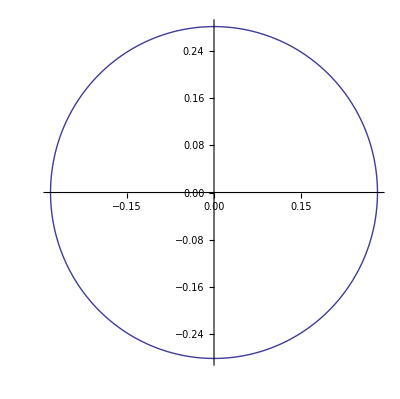

```mathematica
l =0; m = 0;
PolarPlot[SphericalHarmonicY[l,m,θ,0],{θ,0,2*Pi}]
```

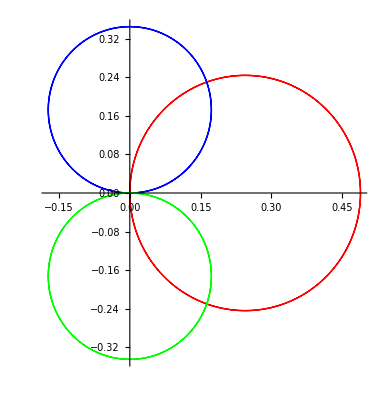

```mathematica
Remove["Global`*"]
Show[PolarPlot[SphericalHarmonicY[l,m,θ,0]/.{l->1,m->0},{θ,0,2*Pi},PlotStyle->{Red}],PolarPlot[SphericalHarmonicY[l,m,θ,0]/.{l->1,m->-1},{θ,0,2*Pi},PlotStyle->{Blue}],PolarPlot[SphericalHarmonicY[l,m,θ,0]/.{l->1,m->1},{θ,0,2*Pi},PlotStyle->{Green}]]
```

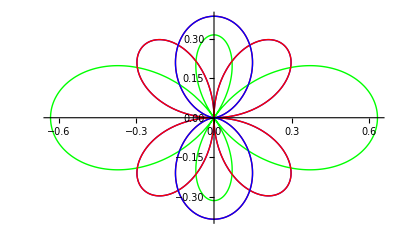

```mathematica
Remove["Global`*"]
Show[PolarPlot[SphericalHarmonicY[l,m,θ,0]/.{l->2,m->-2},{θ,0,2*Pi},PlotStyle->{Red}],PolarPlot[SphericalHarmonicY[l,m,θ,0]/.{l->2,m->-1},{θ,0,2*Pi},PlotStyle->{Blue}],PolarPlot[SphericalHarmonicY[l,m,θ,0]/.{l->2,m->0},{θ,0,2*Pi},PlotStyle->{Green}],PolarPlot[SphericalHarmonicY[l,m,θ,0]/.{l->2,m->1},{θ,0,2*Pi},PlotStyle->{Red}],PolarPlot[SphericalHarmonicY[l,m,θ,0]/.{l->2,m->2},{θ,0,2*Pi},PlotStyle->{Blue}]
]
```

checking the orthonormality

```mathematica
Table[
Table[
Integrate[
Integrate[
SphericalHarmonicY[l,m,θ,ϕ]*SphericalHarmonicY[l1,m1,θ,ϕ],
{ϕ,0,2*Pi},Assumptions->Element[ϕ,Reals]]*Sin[θ],
{θ,Pi,0},Assumptions->Element[θ,Reals]],
{m,-1,1},{m1,-1,1}],
{l,1,2},{l1,1,2}]
```

{{{{0,0,1},{0,-1,0},{1,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,1},{0,-1,0},{1,0,0}}}}

```mathematica
Table[
Table[
Integrate[
Integrate[
SphericalHarmonicY[l,m,θ,ϕ]*SphericalHarmonicY[l1,m1,θ,ϕ]*Sin[θ],
{θ,0,Pi},Assumptions->Element[θ,Reals]],
{ϕ,0,2*Pi},Assumptions->Element[ϕ,Reals]],
{m,-1,1},{m1,-1,1}],
{l,1,2},{l1,1,2}]
```

{{{{0,0,-1},{0,1,0},{-1,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,-1},{0,1,0},{-1,0,0}}}}

```mathematica
l=1;l1=1;m=-1;m1=1;
Integrate[
Integrate[
SphericalHarmonicY[l,m,θ,ϕ]*SphericalHarmonicY[l1,m1,θ,ϕ]*Sin[θ],
{θ,Pi,0},Assumptions->Element[θ,Reals]],
{ϕ,0,2*Pi},Assumptions->Element[ϕ,Reals]]
```

1

```mathematica
l=1;l1=1;m=-1;m1=1;
Integrate[
Integrate[
SphericalHarmonicY[l,m,θ,ϕ]*SphericalHarmonicY[l1,m1,θ,ϕ]*Sin[θ],
{ϕ,0,2*Pi},Assumptions->Element[ϕ,Reals]],
{θ,Pi,0},Assumptions->Element[θ,Reals]]
```

1

```mathematica
Table[
Table[
KroneckerDelta[l,l1]*KroneckerDelta[m,m1],
{m,-1,1},{m1,-1,1}],
{l,1,2},{l1,1,2}]
```

{{{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{1,0,0},{0,1,0},{0,0,1}}}}

question #4

```mathematica
Table[FullSimplify[Total[Table[FullSimplify[Conjugate[SphericalHarmonicY[l,m,θ,ϕ]]*SphericalHarmonicY[l,m,θ,ϕ]],{m,-l,l}]],Assumptions->Element[{θ,ϕ},Reals]],{l,0,3}]
```

{1/(4 π),3/(4 π),5/(4 π),7/(4 π)}

```mathematica
Table[(2*l+1)/(4*Pi),{l,0,3}]
```

{1/(4 π),3/(4 π),5/(4 π),7/(4 π)}

question #5

```mathematica
Table[
FullSimplify[
Total[
Table[
Conjugate[SphericalHarmonicY[l,m,θ1,ϕ1]]*SphericalHarmonicY[l,m,θ,ϕ]
,{m,-l,l}]
]
,Assumptions->Element[{θ,ϕ,θ1,ϕ1},Reals]]
,{l,0,2}]
(*FullSimplify[,Assumptions->Element[{θ,ϕ,θ1,ϕ1},Reals]*)
```

{1/(4 π),(3 (Cos[θ] Cos[θ1]+Cos[ϕ-ϕ1] Sin[θ] Sin[θ1]))/(4 π),1/(64 π)5 (1+3 Cos[2 θ1]+Cos[2 θ] (3+9 Cos[2 θ1])+12 Cos[2 ϕ-2 ϕ1] Sin[θ]^2 Sin[θ1]^2+12 Cos[ϕ-ϕ1] Sin[2 θ] Sin[2 θ1])}

```mathematica
cosΩ = Cos[θ]*Cos[θ1]+Sin[θ]*Sin[θ1]*Cos[ϕ-ϕ1];
Table[(2*l+1)/(4*Pi)*FullSimplify[LegendreP[l,cosΩ],Assumptions->Element[{θ,ϕ,θ1,ϕ1},Reals]]
,{l,0,2}]
```

{1/(4 π),(3 (Cos[θ] Cos[θ1]+Cos[ϕ-ϕ1] Sin[θ] Sin[θ1]))/(4 π),(5 (-1+3 (Cos[θ] Cos[θ1]+Cos[ϕ-ϕ1] Sin[θ] Sin[θ1])^2))/(8 π)}